```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={a1->Subscript[a, 1],a2->Subscript[a, 2],a3->Subscript[a, 3],κi->Subscript[κ, i],κr->Subscript[κ, r],kx->Subscript[k, x], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b1->Subscript[b, 1],b2->Subscript[b, 2],b3->Subscript[b, 3]};
Clear[mu,sgn];
ass=Assumptions->{ky,kz,κi,κr,μ,en,mu,sgn}∈ Reals &&  k>0  && v>0 &&  mu>0;
```

## Definition

```mathematica
DirectionParametricPlot[fun_, {t_, t0_, t1_}, opts___?OptionQ] := 
	Module[{x,y,z,funl, fp, aheads, asize, anumber, color, pp, gr, vars, arrow, data, dt = N[t1 - t0], ps, psdata, dpts, plotfun, plotrange}, 
	funl = ReleaseHold[Hold[fun] /. {Integrate -> NIntegrate, Tooltip[a_]->a}]//Quiet;
	If[VectorQ[funl],funl = ReleaseHold[{Hold[funl]}]];
	If[Head[funl] === Piecewise, funl = {funl}];
	If[MatrixQ[First[funl]], funl = Flatten[funl,1]];
	If[Not[MatrixQ[funl/.t->t0]] & , Return[Message[dpp::improperinput]]];
        {aheads, anumber, color} = 
	    {"DrawArrowheads", "ArrowNumber", ColorFunction} /. {opts} /.  
               Options[DirectionParametricPlot];		
     If[anumber <= 0, aheads = False];
     {ps,asize}=AppendOptions[DirectionParametricPlot,{PlotStyle,"ArrowSize"}, Length[funl],opts]; 
asize = If[Head[#] === Symbol,{#},{.05#}] & /@ (Last/@asize);
     vars = {x,y};
     arrow = (Arrow[#]&); 

     If[Not[FreeQ[ps, RGBColor[_,_,_] | Hue[_] | GrayLevel[_]]], color =None];
     If[MatchQ[color, Automatic],  
                 color = Function[Flatten[{vars,t}]//Evaluate, Hue[.9 t]]];		
     aheads = 
	If[aheads,fp = D[funl, t];
          If[FreeQ[fp, Derivative, Infinity], 			
	If[color === None, psdata = 
 {RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051],
RGBColor[0.560181, 0.691569, 0.194885], RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
		RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], RGBColor[0.571589, 0.586483, 0.], 
		RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609, 0.52200666434, 0.85], 
		RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], RGBColor[0.736782672705901, 0.358, 0.5030266573755369], 
		RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]
		};
	     ps = MapThread[Flatten[{#1,#2}]&,{psdata[[1;;Length[funl]]],ps}];
	     ps1 = DeleteCases[ ps, Thickness[_]|Tube[_], Infinity]; 
data = Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], {t, t0 + dt/anumber, t1, dt/(anumber+.0001)}];
data = Map[MapThread[Flatten[{Arrowheads[Last[Flatten[{#2}]]],#1,#3}]&,{ps1,asize,#}]&,data],
			
acolor= Table[color[Sequence@@Flatten[{vars,(t - t0)/dt}]],{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
asizes=Map[Arrowheads,asize,{2}]; 
arrows=Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], 
										{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
data=MapThread[{#1,#2}&,{acolor,(Transpose[Flatten/@{asizes,#}]&/@arrows)}]];
              Select[data, FreeQ[#, Indeterminate, Infinity] &, Infinity],
              Message[dpp::noderiv];{}],{}];

Show[	
	ParametricPlot[funl//Evaluate, {t, t0, t1}, ColorFunction -> color, PlotStyle -> ps,
				Sequence @@ FilterRules[{opts}, Options[ParametricPlot]] // Evaluate], 
	Graphics[aheads],  Sequence@@FilterRules[{opts},Options[Graphics]]//Evaluate,
   PlotRangePadding->Scaled[.04]]
	]

Options[DirectionParametricPlot]=
{"ArrowNumber"->15,"ArrowSize"->Large,ColorFunction->Automatic,"DrawArrowheads"->True,PlotStyle->Automatic};

dpp::noderiv="Mathematica was unable to find the derivative which is used to produce the arrowheads. Plotting will proceed without arrowheads. ";

dpp::improperinput="The input function is not a vector or a list of vectors. ";
AppendOptions[command_Symbol,options_,rest__]:=AppendOptions[command,{options},rest]
AppendOptions[command_Symbol,{options__},number_?(IntegerQ[#]&&NonNegative[#]&),opts___Rule]:=AppendOptions[command,{options},Table[number,{Length[{options}]}],opts]
AppendOptions[command_Symbol,{options__},numbers_?(VectorQ[#,(IntegerQ[#]&&NonNegative[#])&]&),opts___Rule]:=Module[{defaultstyles,userstyles,lengths,newstyles},defaultstyles={options}/.Options[command];
userstyles={options}/.{opts}/.Options[command];
userstyles=(If[ListQ[#],#,{#}]&/@userstyles)/.{}->{{}};
lengths=Length/@userstyles;
newstyles=MapThread[MapThread[Flatten[{#1,#2}]&,{Table[#1,{#2}],#3}]&,{defaultstyles,lengths,userstyles}];
newstyles=MapThread[Join[Flatten[Table[#1,{Floor[#2/#3]}],1],Take[#1,Mod[#2,#3]]]&,{newstyles,numbers,lengths}];
With[{temp=DeleteCases[newstyles,Automatic,Infinity]},If[Length[{options}]===1,First[temp],temp]]]
```

## Weyl

```mathematica
enfa=(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2);
FullSimplify[Solve[enfa==mu,ky],ass]
FullSimplify[Solve[enfa==mu,kz],ass]
```

{{ky→(mu+a2^2 (kz+mu)-kz √(1-(1+a2^2) η^2))/(a2 (1+√(1-(1+a2^2) η^2)))}}

{{kz→(mu+a2^2 mu-a2 ky (1+√(1-(1+a2^2) η^2)))/(-a2^2+√(1-(1+a2^2) η^2))}}

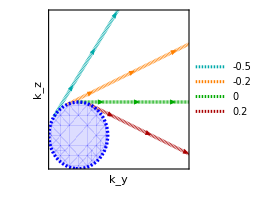

```mathematica
lim=π;mu=0.5;th=0.012;η=0.4;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.001]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Red],Thickness[th],Dashing[0.001]]};
fs=RegionPlot[(kz^2+ky^2)(1-η^2)<mu^2,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
a2v={-0.5,-0.2,0,0.2};
(*******{en->(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2), κr->(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))} **********)
i=1;a2=a2v[[i]];
c1=DirectionParametricPlot[{ky,(-a2 ky (1+√(1-(1+a2^2) η^2))+mu+a2^2 mu)/(-a2^2+√(1-(1+a2^2) η^2))},{ky,-0.5,lim},"ArrowSize"->1.2,PlotRange->{{-0.1,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2))>0 ],PlotStyle->style[[i]],"ArrowNumber"->9];
(*********)
i=2;a2=a2v[[i]];
c2=DirectionParametricPlot[{ky,(-a2 ky (1+√(1-(1+a2^2) η^2))+mu+a2^2 mu)/(-a2^2+√(1-(1+a2^2) η^2))},{ky,-0.5,lim+1},"ArrowSize"->1.2,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2))>0 ],PlotStyle->style[[i]],"ArrowNumber"->6];
(*********)
i=3;a2=a2v[[i]];
c3=DirectionParametricPlot[{ky,(-a2 ky (1+√(1-(1+a2^2) η^2))+mu+a2^2 mu)/(-a2^2+√(1-(1+a2^2) η^2))},{ky,-0.2,lim},"ArrowSize"->1.2,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2))>0 ],PlotStyle->style[[i]],"ArrowNumber"->5];
(***************)
i=4;a2=a2v[[i]];
c4=DirectionParametricPlot[{ky,(-a2 ky (1+√(1-(1+a2^2) η^2))+mu+a2^2 mu)/(-a2^2+√(1-(1+a2^2) η^2))},{ky,-0.05,lim+1},"ArrowSize"->1.2,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2))>0 ],PlotStyle->style[[i]],"ArrowNumber"->6];
pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->200,PlotRange->{{-0.5,2},{-0.5,2}}];
leg=LineLegend[style,{a2v[[1]], a2v[[2]], a2v[[3]], a2v[[4]]},LabelStyle->{14,Darker[Brown],Bold},LegendLayout->{"Row",1}];

(**********)
plt=Legended[Graphics[pl],Placed[leg,Below]]
Clear[kx,mu,kw,a2,η];
SetDirectory[NotebookDirectory[]];
Export["weyl.pdf",Rasterize[plt],ImageResolution->100];
```

## TSM

```mathematica
enfa=-kz+(2 √2 b1 ky+4 kz)/(2+b1^2);
FullSimplify[Solve[enfa==mu,ky],ass]
FullSimplify[Solve[enfa==mu,kz],ass]
```

{{ky→((-2+b1^2) kz+(2+b1^2) mu)/(2 √2 b1)}}

{{kz→(2 (√2 b1 ky-2 mu))/(-2+b1^2)-mu}}

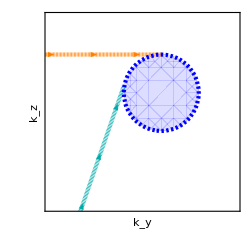

```mathematica
lim=π;mu=0.5;th=0.012;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.001]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Red],Thickness[th],Dashing[0.001]]};
fs=RegionPlot[(kz^2+ky^2)<mu^2,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
b1=-1;
(*{en->-kz+(2 √2 b1 ky+4 kz)/(2+b1^2),κr->((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2),κi->0,a1->0,a2->-b1^2/2,b2->0}*)
i=1;
c1=DirectionParametricPlot[{ky,(2 (√2 b1 ky-2 mu))/(-2+b1^2)-mu}(*{((-2+b1^2) kz+(2+b1^2) mu)/(2 √2 b1),kz}*),{ky,-1.5,-0.5},"ArrowSize"->1.2,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},(-2+b1^2) ky+2 √2 b1 kz>0 ],PlotStyle->style[[i]],"ArrowNumber"->4.35];
(*********)
i=2;
c2=DirectionParametricPlot[{ky,mu},{ky,-lim,0},"ArrowSize"->1.2,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},-ky>0 ],PlotStyle->style[[i]],"ArrowNumber"->5.5];
(*********)
pl=Show[c1,c2,fs,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->250,PlotRange->{{-1.5,1},{-1.5,1}}]
(**********)
SetDirectory[NotebookDirectory[]];
Export["tsm.pdf",Rasterize[pl],ImageResolution->100];
Clear[b1,mu];
```

## RSW

```mathematica
(* {en->(3 kx)/2-(2 kx^3)/(kx^2+ky^2),κr->ky-(4 kx^2 ky)/(kx^2+ky^2)} or {en->-(3 kx)/2+(2 kx^3)/(kx^2+ky^2),κr->ky (-1+(4 kx^2)/(kx^2+ky^2))} *)
```

```mathematica
(3 kx)/2-(2 kx^3)/(kx^2+ky^2)==kx(3  ky^2- kx^2)/(2 (kx^2+ky^2))//FullSimplify
```

True

```mathematica
Clear[sgn,mu];enfa=sgn kx(3  kysq- kx^2)/(2 (kx^2+kysq));
FullSimplify[Solve[enfa==mu,kysq],ass]
FullSimplify[Solve[sgn kx(3  ky^2- kx^2)/(2 (kx^2+ky^2))==mu,kx],ass]/.{sgn^2->1,sgn^6->1}
```

{{kysq→(kx^2 (2 mu+kx sgn))/(-2 mu+3 kx sgn)}}

{{kx→-(2 mu+(9 ky^2+4 mu^2)/((54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))+(54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))/(3 sgn)},{kx→(-4 mu+((1+ⅈ √3) (9 ky^2+4 mu^2))/((54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))+(1-ⅈ √3) (54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))/(6 sgn)},{kx→(-4 mu+((1-ⅈ √3) (9 ky^2+4 mu^2))/((54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))+(1+ⅈ √3) (54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))/(6 sgn)}}

```mathematica
mu=0.5;sgn=-1;Clear[g,data,arr4];g[ky_]:=Chop[2mu/3];
data=Table[{g[ky],ky},{ky,3,-0.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr4=p0/. Line[ky_]:>{Arrowheads[Table[.05,{4}]],Arrow[ky]};
cc1=ContourPlot[ 3kx/2==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->Green,RegionFunction->Function[{kx,ky,z},ky>0  ]]//Quiet;
Show[cc1,arr3,RegionFunction->Function[{kx,ky,z},-sgn (3 kx^2 ky-ky ky^2)>0]]
```

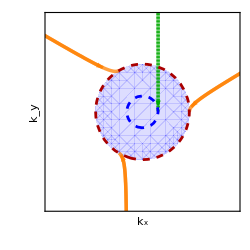

```mathematica
mu=0.5;sgn=-1;th=0.01;

style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.0025]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.0025]]};

(*********)
rp=RegionPlot[√(ky^2+kx^2)<2mu,{kx,-lim,lim},{ky,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->None];
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed],Directive[Blue,Dashed]}];
(***********)
Clear[f,data];f[kx_]=kx √((2 mu+sgn kx)/(-2 mu+3 sgn kx));
data=Table[{kx,f[kx]},{kx,π+1,1,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr1=p0/. Line[kx_]:>{Arrowheads[Table[.06,{8}]],Arrow[kx]};
c1=ContourPlot[ -sgn kx(kx^2-3  ky^2)/(2 (kx^2+ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[2]],RegionFunction->Function[{kx,ky,z},-sgn (3 kx^2 ky-ky ky^2)>0  ]]//Quiet;
(********************)
Clear[f,data];f[kx_]=-kx √((2 mu+sgn kx)/(-2 mu+3 sgn kx));
data=Table[{kx,f[kx]},{kx,-π,-0.8,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr2=p0/. Line[kx_]:>{Arrowheads[Table[.06,{6}]],Arrow[kx]};
(*********)
Clear[g,data,arr3];g[ky_]:=Chop[(-4 mu+((1-ⅈ √3) (9 ky^2+4 mu^2))/((54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))+(1+ⅈ √3) (54 ky^2 mu+8 mu^3+3 √(-81 ky^6+48 ky^2 mu^4+216 ky^4 mu^2 sgn^4))^(1/3))/(6 sgn)];
data=Table[{g[ky],ky},{ky,-3,0,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr3=p0/. Line[ky_]:>{Arrowheads[Table[.06,{6}]],Arrow[ky]};
(**************)
i=2;
Clear[g,data,arr4];g[ky_]=Chop[2mu/3];
data=Table[{g[ky],ky},{ky,3.1,0.1,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->Directive[Darker[Green],Thickness[th],Dashing[0.001]]];
arr4=p0/. Line[ky_]:>{Arrowheads[Table[.06,{6}]],Arrow[ky]};
c4=Quiet[ContourPlot[(*-(3 kx)/2*)3/2 kx==mu,{kx,-lim,lim},{ky,-lim,lim},RegionFunction->Function[{kx,ky,z},Chop[(*-ky*)ky]>0 ],ContourStyle->Directive[Darker[Green],Thickness[th],Dashing[0.001]]]];
(*********)
pl=Show[rp,arr1,arr2,arr3,arr4,c1,c4,fs,Frame->True,Axes->False,FrameTicks->None,PlotRange->{{-2,2},{-2,2}},LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_x","k_y"},ImageSize->250]
(**********)
SetDirectory[NotebookDirectory[]];
Export["rsw.pdf",Rasterize[pl],ImageResolution->100];
Clear[b1,mu];
```

## 2-band Hopf

```mathematica
ass=Assumptions->{ξ,vz,vp,ky,kz,ek,b,κi,κr}∈ Reals &&  k>0 && kp>0 && ek>0 && vp>0 && vz>0;enfa=(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2;
FullSimplify[Solve[enfa==μ,ky],ass]
FullSimplify[Solve[enfa==μ,kz],ass]
```

{{ky→-((-1+b^2) kz vz)/(2 b vp)+(b μ)/(2 kz vp vz)}}

{{kz→(b (-ky vp+√(ky^2 vp^2+(-1+b^2) μ)))/((-1+b^2) vz)},{kz→(b (ky vp+√(ky^2 vp^2+(-1+b^2) μ)))/(vz-b^2 vz)}}

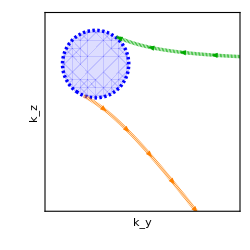

```mathematica
mu=0.5;lim=π;vp=1;vz=1;b=2;kx=0;th=0.01;kw=1;
style={Directive[Darker[Cyan],Thickness[th]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]]};
rp=RegionPlot[(kx^2+ky^2) vp^2+((kz))^2 vz^2<mu,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];

(*pp1=DirectionParametricPlot[{-((-1+b^2) kz vz)/(2 b vp)+(b mu)/(2 kz vp vz),kz},{kz,-lim,lim},"ArrowSize"->1,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},(ky-((kz) vz)/(b vp))>0 ],PlotStyle->style[[2]],"ArrowNumber"->5];*)
pp1=DirectionParametricPlot[{ky,(b (ky vp+√(ky^2 vp^2+(-1+b^2) mu)))/(vz-b^2 vz)},{ky,-0.25,lim},"ArrowSize"->1,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},(ky-((kz) vz)/(b vp))>0 ],PlotStyle->style[[2]],"ArrowNumber"->7];
pp2=DirectionParametricPlot[{-ky,(b (ky vp+√(ky^2 vp^2+(-1+b^2) mu)))/((-1+b^2) vz)},{ky,-lim,-0.44},"ArrowSize"->1,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,RegionFunction->Function[{ky,kz,z},(ky-((kz) vz)/(b vp))>0 ],PlotStyle->style[[4]],"ArrowNumber"->4];
pl=Show[rp,pp1,pp2,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->250,PlotRange->{{-1,3},{-3,1}}]
Clear[b,vz,vp,kx];
SetDirectory[NotebookDirectory[]];
Export["dipole1.pdf",Rasterize[pl],ImageResolution->100];
```

## 3-band Hopf

```mathematica
FullSimplify[Solve[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)==μ,kz],ass]
FullSimplify[Solve[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)==μ,ky],ass]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kz→-√μ √(-2 b1 ky+μ+b1^2 μ)},{kz→√μ √(-2 b1 ky+μ+b1^2 μ)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ky→(-kz^2+(1+b1^2) μ^2)/(2 b1 μ)}}

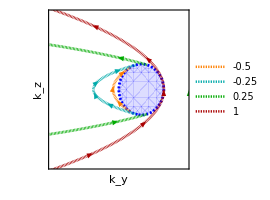

```mathematica
lim=π;mu=0.5;th=0.01;
style={Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Cyan],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Red],Thickness[th],Dashing[0.001]]};
b1v={-0.5,-0.25,0.25,1};
fs=RegionPlot[ky^2+kz^2<mu^2,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
(************)
i=1;
b1=b1v[[i]];
c1=DirectionParametricPlot[{(-kz^2+(1+b1^2) mu^2)/(2 b1 mu),kz},{kz,-0.5,0.5},"ArrowSize"->Medium,"ArrowNumber"->3.5,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,PlotStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ]]//Quiet;
(************)
i=2;
b1=b1v[[i]];
c2=DirectionParametricPlot[{(-kz^2+(1+b1^2) mu^2)/(2 b1 mu),kz},{kz,-0.5,0.5},"ArrowSize"->Medium,"ArrowNumber"->4.5,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,PlotStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ]]//Quiet;
(************)
i=3;
b1=b1v[[i]];
c3=DirectionParametricPlot[{(-kz^2+(1+b1^2) mu^2)/(2 b1 mu),kz},{kz,-lim,lim},"ArrowSize"->Medium,"ArrowNumber"->10,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,PlotStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ]]//Quiet;
(************)
i=4;
b1=b1v[[i]];
c4=DirectionParametricPlot[{(-kz^2+(1+b1^2) mu^2)/(2 b1 mu),kz},{kz,-lim,lim},"ArrowSize"->Medium,"ArrowNumber"->10,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,PlotStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ]]//Quiet;
(************)
pl=Show[fs,c1,c2,c3,c4,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->200,PlotRange->{{-2,1},{-1.5,1.5}}];
leg=LineLegend[style,{b1v[[1]], b1v[[2]], b1v[[3]], b1v[[4]]},LabelStyle->{14,Darker[Brown],Bold},LegendLayout->{"Row",2}];

(**********)
plt=Legended[Graphics[pl],Placed[leg,Below]]
Clear[kx,mu,b1v,i,b1];
SetDirectory[NotebookDirectory[]];
Export["dipole2.pdf",Rasterize[plt],ImageResolution->100];
```

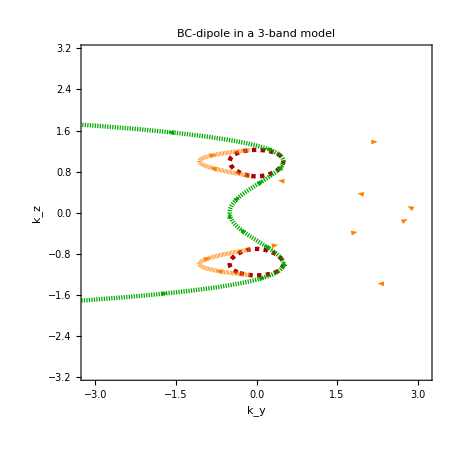

```mathematica
lim=π;mu=0.5;kw=1;th=0.007;
style={Directive[Darker[Cyan],Thickness[th]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};

b1v={-0.5,-0.25,0.25,1};
(************)
i=2;
b1=b1v[[i]];
c2=DirectionParametricPlot[{(- (kz^2-kw^2)^2+(1+b1^2) mu^2)/(2 b1 mu),kz},{kz,-lim,lim},"ArrowSize"->Medium,"ArrowNumber"->25,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,PlotStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √((kz^2-kw^2)^2+b1^2 (mu^2))]>=0 ]]//Quiet;
(************)
i=4;
b1=b1v[[i]];
c4=DirectionParametricPlot[{(- (kz^2-kw^2)^2+(1+b1^2) mu^2)/(2 b1 mu),kz},{kz,-lim,lim},"ArrowSize"->Medium,"ArrowNumber"->20,PlotRange->{{-lim,lim},{-lim,lim}},Axes->False, Frame->True,PlotStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √((kz^2-kw^2)^2+b1^2 (mu^2))]>=0 ]]//Quiet;
(************)
fs=ContourPlot[ky^2+ (kz^2-kw^2)^2==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];
(*******)
pl=Show[fs,c2,c4,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"BC-dipole in a 3-band model",20,FontFamily->"TexMaths Roman",Brown,Bold]]
Clear[kx,mu,kw,b1v,i,b1];
SetDirectory[NotebookDirectory[]];
```

## Double-Weyl

```mathematica
Clear[mu,t,enfa];
enfa=(kz √(Cos[t]^2-4 ky^4 Tan[t]^2/kz^2))/Cos[t];
FullSimplify[Solve[enfa==mu,kz],ass]
FullSimplify[Solve[-enfa==mu,kz],ass]
FullSimplify[Solve[(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t]==mu,kz],ass]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kz→-√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2)},{kz→√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kz→-√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2)},{kz→√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kz→-√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2)},{kz→√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2)}}

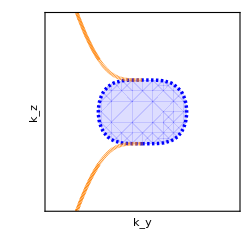

```mathematica
mu=0.5;lim=π;th=0.01;t=π/6;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.001]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Red],Thickness[th],Dashing[0.001]]};
fs=RegionPlot[(ky^2)^2+(kz)^2<mu^2,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
b1=-1;
(***************)
Clear[f,data];f[ky_]=√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2);
data=Table[{ky,f[ky]},{ky,-0.7,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr1=p0/. Line[ky_]:>{Arrowheads[Table[.06,{5.5}]],Arrow[ky]};
c1=ContourPlot[(√(kz^2 Cos[t]^2-4 ky^4 Tan[t]^2))/Cos[t]==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[2]], PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},kz^2 Cos[t]^2-4 ky^4 Tan[t]^2>=0 && -ky/Cos[t]>0]]//Quiet;
(*********)
Clear[f,data];f[ky_]=-√(mu^2+(4 ky^4 Tan[t]^2)/Cos[t]^2);
data=Table[{ky,f[ky]},{ky,-0.7,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr2=p0/. Line[ky_]:>{Arrowheads[Table[.06,{6.5}]],Arrow[ky]};
(*********)
pl=Show[fs,arr1,arr2,c1,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->250,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
(**********)
SetDirectory[NotebookDirectory[]];
Export["double-weyl.pdf",Rasterize[pl],ImageResolution->100];
Clear[t,f,mu];
```

## Triple-Weyl

```mathematica
Clear[mu,t,enfa];
enfa=1/3 √(9(kz)^2-(512 ky^6)/3);
FullSimplify[Solve[enfa==mu,kz],ass]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kz→-(√(512 ky^6+27 mu^2))/(3 √3)},{kz→(√(512 ky^6+27 mu^2))/(3 √3)}}

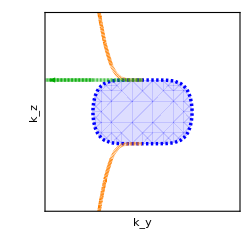

```mathematica
mu=0.5;lim=π;th=0.01;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.001]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Red],Thickness[th],Dashing[0.001]]};
fs=RegionPlot[(ky^2)^3+(kz)^2<mu^2,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
(***************)
Clear[f,data];f[ky_]=(√(512 ky^6+27 mu^2))/(3 √3);
data=Table[{ky,f[ky]},{ky,-0.5,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr1=p0/. Line[ky_]:>{Arrowheads[Table[.06,{35.5}]],Arrow[ky]};
c1=ContourPlot[1/3 √(9(kz)^2-(512 ky^6)/3)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[2]], PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},-ky>0 && -(512 ky^6)/3+9 (kz)^2>=0]]//Quiet;
(*********)
Clear[f,data];f[ky_]=-(√(512 ky^6+27 mu^2))/(3 √3);
data=Table[{ky,f[ky]},{ky,-0.5,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[2]]];
arr2=p0/. Line[ky_]:>{Arrowheads[Table[.06,{35.5}]],Arrow[ky]};
(*********)
Clear[f,data];f[ky_]=mu;
data=Table[{ky,f[ky]},{ky,-0.8,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style[[3]]];
arr3=p0/. Line[ky_]:>{Arrowheads[Table[.06,{2}]],Arrow[ky]};
c3=ContourPlot[(kz)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[3]], RegionFunction->Function[{ky,kz,z},-ky>0 ]]//Quiet;
(**************)
pl=Show[fs,arr1,arr2,arr3,c1,c3,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->250,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
(**********)
SetDirectory[NotebookDirectory[]];
Export["triple-weyl.pdf",Rasterize[pl],ImageResolution->100];
Clear[b1,mu];
```

## Charge-4 Weyl

```mathematica
Clear[mu,enfa];
enfa=((ky-kz) (ky+kz) v)/(√(1+v^2));
FullSimplify[Solve[enfa==mu,kz],ass]
FullSimplify[Solve[enfa==mu,ky],ass]
```

{{kz→-√(ky^2-√2 mu)},{kz→√(ky^2-√2 mu)}}

{{ky→-√(kz^2+√2 mu)},{ky→√(kz^2+√2 mu)}}

```mathematica
lim=π;mu=1.3;v=1;Quiet[ContourPlot[((ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},RegionFunction->Function[{ky,kz,z},Chop[ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic]]
```

```mathematica
mu=0.5;lim=π;th=0.01;style=Directive[Darker[Green],Thickness[th],Opacity[0.75]];
v=1;
fs1=RegionPlot[(v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2)<mu^2 && -ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2>=0,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
(***************)
Clear[f,data];f[ky_]=-√(ky^2-(mu √(1+v^2))/v);
data=Table[{ky,f[ky]},{ky,-1.2,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr1=p0/. Line[ky_]:>{Arrowheads[Table[.08,{2}]],Arrow[ky]};
(***************)
Clear[g,data];g[kz_]=-√(kz^2-(mu √(1+v^2))/v);
data=Table[{g[kz],kz},{kz,1.2,1.5,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr3=p0/. Line[kz_]:>{Arrowheads[Table[.08,{2}]],Arrow[kz]};

(************)
Clear[f,data];f[ky_]=√(ky^2-(mu √(1+v^2))/v);
data=Table[{ky,f[ky]},{ky,1.2,1.5,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr2=p0/. Line[ky_]:>{Arrowheads[Table[.08,{2}]],Arrow[ky]};
(***************)
Clear[g,data];g[kz_]=√(kz^2-(mu √(1+v^2))/v);
data=Table[{g[kz],kz},{kz,-1.2,-1.5,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr4=p0/. Line[kz_]:>{Arrowheads[Table[.08,{2}]],Arrow[kz]};

(************)

c1=Quiet[ContourPlot[((ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
c2=Quiet[ContourPlot[(-(ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[-ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
pl1=Show[c1,c2,arr1,arr2,arr3,arr4,fs1,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->250,PlotRange->{{-1.42,1.42},{-1.42,1.42}},Epilog->Style[Text["v =  1",{0,1.2}],20,FontFamily->"TexMaths Symbols",Brown,Bold]]
```

```mathematica
(***************)
v=4;
fs1=RegionPlot[(v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2)<mu^2&& -ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2>=0,{ky,-lim,lim},{kz,-lim,lim},PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],BoundaryStyle->Directive[Blue,Dashing[0.007],Thickness[th]]];
(************)
Clear[f,data];f[ky_]=-√(ky^2-(mu √(1+v^2))/v);
data=Table[{ky,f[ky]},{ky,-0,-lim,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr1=p0/. Line[ky_]:>{Arrowheads[Table[.08,{10}]],Arrow[ky]};
(************)
Clear[f,data];f[ky_]=√(ky^2-(mu √(1+v^2))/v);
data=Table[{ky,f[ky]},{ky,0,lim,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr2=p0/. Line[ky_]:>{Arrowheads[Table[.08,{10}]],Arrow[ky]};
(************)
Clear[g,data];g[kz_]=√(kz^2-(mu √(1+v^2))/v);
data=Table[{g[kz],kz},{kz,-1,-lim,-0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr3=p0/. Line[kz_]:>{Arrowheads[Table[.08,{10}]],Arrow[kz]};
(************)
Clear[g,data];g[kz_]=-√(kz^2-(mu √(1+v^2))/v);
data=Table[{g[kz],kz},{kz,1,lim,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->style];
arr4=p0/. Line[kz_]:>{Arrowheads[Table[.08,{10}]],Arrow[kz]};
(************)

c1=Quiet[ContourPlot[((ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0]]];
c2=Quiet[ContourPlot[(-(ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[-ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0]]];
(***********)
pl2=Show[c1,c2,arr1,arr2,arr3,arr4,fs1,Frame->True,Axes->False,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->250,PlotRange->{{-1,1},{-1,1}},Epilog->Style[Text["v =  4",{0,0.88}],20,FontFamily->"TexMaths Symbols",Brown,Bold]]
```

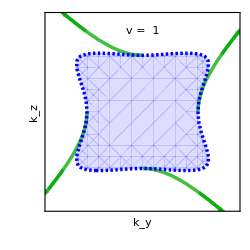
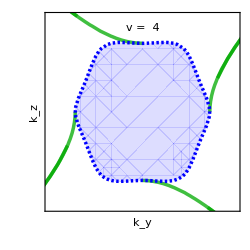
```mathematica
pl1=-Graphics-;pl2=-Graphics-;plt=GraphicsRow[{pl1,pl2}, ImageSize->500];
Clear[kx,v,a1,b1];
SetDirectory[NotebookDirectory[]];
Export["qweyl.pdf",Rasterize[plt],ImageResolution->100];
```

## Monopole-Dipole plots

```mathematica
lim=π;
Ωmon={kx/((ky^2+kz^2)^2),ky/((ky^2+kz^2)^2),kz/((ky^2+kz^2)^2)};
Ωdip=kz{kx/((ky^2+kz^2)^2),ky/((ky^2+kz^2)^2),kz/((ky^2+kz^2)^2)};
(********)
arr=Graphics3D[{Directive[Darker[Red],Specularity[1,20]],Arrowheads[{-0.07,0.07}],Arrow[Tube[{{0,0,-0.45},{0,0,0.45}}(**),Scaled[0.01]]]},Boxed->False,Axes->False,Epilog->Text[Style["BC-monopole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250];
p01=SliceVectorPlot3D[Ωmon,{"CenterCutSphere", π/2.2+ 0.15},{kx,-1,1},{ky,-1,1},{kz,-1,1},Ticks->None,Boxed->False,Axes->False,ViewPoint->{2.4968637195854337,-1.9921679189100223,1.1166640267706789},VectorStyle->Directive[Darker[Cyan],Opacity[0.75]],VectorColorFunction->None,Epilog->Text[Style["BC-monopole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250];
p1=Show[p01,arr,Epilog->Text[Style["BC-monopole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250]
(******)
arr=Graphics3D[{Directive[Darker[Red],Specularity[1,20]],Arrowheads[0.07],Arrow[Tube[{{0,0,-0.35},{0,0,0.35}}(**),Scaled[0.01]]]},Boxed->False,Axes->False,Epilog->Text[Style["BC-monopole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250];
p02=SliceVectorPlot3D[Ωdip,{"CenterCutSphere", π/2.2+ 0.15},{kx,-1,1},{ky,-1,1},{kz,-1,1},Ticks->None,Boxed->False,Axes->False,ViewPoint->{2.4968637195854337,-1.9921679189100223,1.1166640267706789},VectorStyle->Directive[Darker[Cyan],Opacity[0.75]],VectorColorFunction->None,Epilog->Text[Style["BC-monopole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250];
p2=Show[p02,arr,Epilog->Text[Style["BC-dipole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250,Epilog->Text[Style["BC-monopole",16,FontFamily->"TexMaths Roman",Brown,Bold],Scaled[{0.5,0.2}](**)],ImageSize->250]
(*plt=GraphicsRow[{p1,p2},Spacings->-60,ImageSize->500]*)

SetDirectory[NotebookDirectory[]];
Export["mono-apl.pdf",Rasterize[p1],ImageResolution->100];
Export["dipole-apl.pdf",Rasterize[p2],ImageResolution->100];
```

-Graphics3D-

-Graphics3D-

```mathematica
AbsoluteOptions[]
```